# Calculation of transmission probability in BLG-TBG-BLG junction

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[x1];
s1=Sign[x1-x2];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
G=x1*ae;
u0=x2*ae;
x2=0.0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
T1=Block[{y1=0},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T2=Block[{y1=0.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T3=Block[{y1=1.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T4=Block[{y1=1.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T5=Block[{y1=2.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T6=Block[{y1=2.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T7=Block[{y1=3.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];
list=AppendTo[list1,{x1,Re[T1],Re[T2],Re[T3],Re[T4],Re[T5],Re[T6],Re[T7]}];
},{x1,-1.111,1.111,0.0002}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG.dat",listn]
```

# Calculation of transmission probability in BLG-SBG-BLG as well as BLG-STBG-BLG junction

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[x1];
s1=Sign[x1-x2];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
G=x1*ae;
u0=x2*ae;
x2=0.1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
T1=Block[{y1=0},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T2=Block[{y1=0.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T3=Block[{y1=1.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T4=Block[{y1=1.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T5=Block[{y1=2.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T6=Block[{y1=2.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T7=Block[{y1=3.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];
list=AppendTo[list1,{x1,Re[T1],Re[T2],Re[T3],Re[T4],Re[T5],Re[T6],Re[T7]}];
},{x1,-1.111,1.111,0.0002}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG2.dat",listn]
```

# Plot of transmission probability in BLG-TBG-BLG junction

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

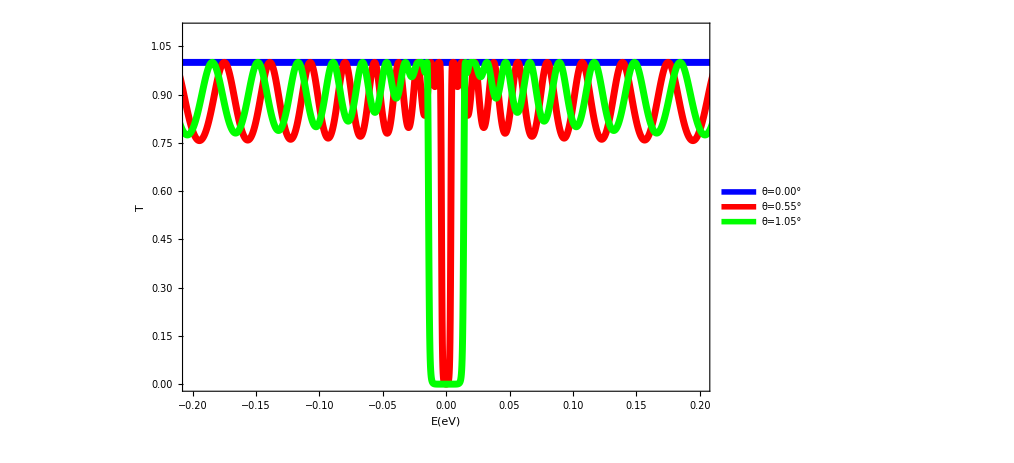

```mathematica
data1=Import["TBG.dat"][[All,{1,2}]];
data2=Import["TBG.dat"][[All,{1,3}]];
data3=Import["TBG.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{-0.2,0.2},{0,1.1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.55°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E(eV)",25,Black],Rotate[Style["T",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of transmission probability in BLG-SBG-BLG and BLG-STBG-BLG junction

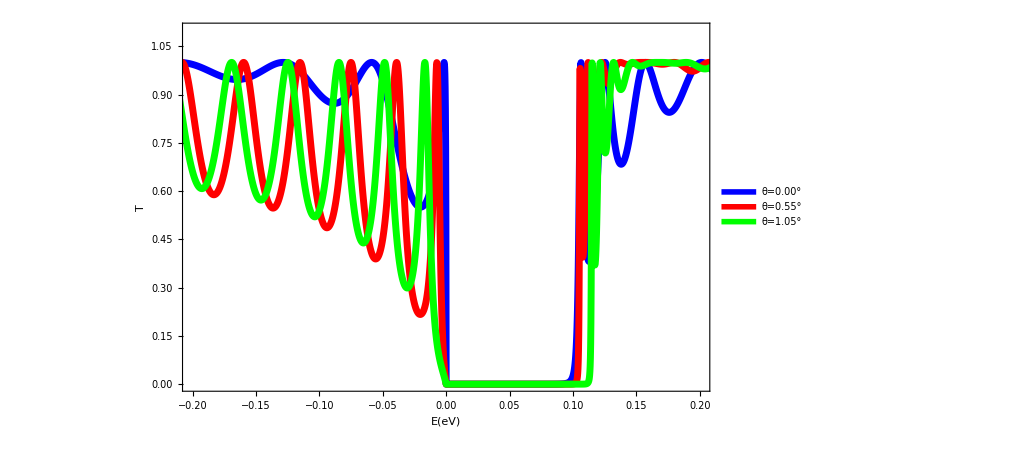

```mathematica
data1=Import["TBG2.dat"][[All,{1,2}]];
data2=Import["TBG2.dat"][[All,{1,3}]];
data3=Import["TBG2.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{-0.2,0.2},{0,1.1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.55°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E(eV)",25,Black],Rotate[Style["T",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Thermoelectric transport calculation both as quantum heat engine and quantum refrigerator in BLG-TBG-BLG junction

```mathematica
Clear["Global`*"]
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
x2=0.0;


R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{y1,gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{y1,0,2,0.01},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran3.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained 7.05297×10^-38+0. ⅈ and 9.44593×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.46937×10^-39+0. ⅈ and 9.03477×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1031,17].

KernelObject::rdead: Discarding kernel 8 (Local).

LaunchKernels::req: Requeueing evaluations {91} assigned to dead kernel 8 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1032,18].

KernelObject::rdead: Discarding kernel 9 (Local).

LaunchKernels::req: Requeueing evaluations {89} assigned to dead kernel 9 (Local).

LaunchKernels::clone: dead kernel 8 (Local) resurrected as kernel 11 (Local).

LaunchKernels::clone: dead kernel 9 (Local) resurrected as kernel 12 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1024,10].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

KernelObject::rdead: Discarding kernel 1 (Local).

General::stop: Further output of KernelObject::rdead will be suppressed during this calculation.

LaunchKernels::req: Requeueing evaluations {84} assigned to dead kernel 1 (Local).

General::stop: Further output of LaunchKernels::req will be suppressed during this calculation.

LaunchKernels::clone: dead kernel 1 (Local) resurrected as kernel 13 (Local).

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

{1883.6,Null}

TBG_tran2.dat

# Thermoelectric transport calculation both as quantum heat engine and quantum refrigerator in BLG-SBG-BLG junction

```mathematica
Clear["Global`*"]
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0.0;


R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{x2,gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{x2,0,0.1,0.001},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran4.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained 7.05297×10^-38+0. ⅈ and 9.44593×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.46937×10^-39+0. ⅈ and 9.03477×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1031,17].

KernelObject::rdead: Discarding kernel 8 (Local).

LaunchKernels::req: Requeueing evaluations {91} assigned to dead kernel 8 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1032,18].

KernelObject::rdead: Discarding kernel 9 (Local).

LaunchKernels::req: Requeueing evaluations {89} assigned to dead kernel 9 (Local).

LaunchKernels::clone: dead kernel 8 (Local) resurrected as kernel 11 (Local).

LaunchKernels::clone: dead kernel 9 (Local) resurrected as kernel 12 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1024,10].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

KernelObject::rdead: Discarding kernel 1 (Local).

General::stop: Further output of KernelObject::rdead will be suppressed during this calculation.

LaunchKernels::req: Requeueing evaluations {84} assigned to dead kernel 1 (Local).

General::stop: Further output of LaunchKernels::req will be suppressed during this calculation.

LaunchKernels::clone: dead kernel 1 (Local) resurrected as kernel 13 (Local).

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

{1883.6,Null}

TBG_tran2.dat

# Thermoelectric transport calculation both as quantum heat engine and quantum refrigerator in BLG-STBG-BLG junction

```mathematica
Clear["Global`*"]
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
gf=0.1;


R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{y1,x2,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{y1,0,2,0.1},{x2,0,0.1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran2.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained 7.05297×10^-38+0. ⅈ and 9.44593×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.46937×10^-39+0. ⅈ and 9.03477×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.59353×10^-20}. NIntegrate obtained -1.76324×10^-38+0. ⅈ and 8.56653×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1031,17].

KernelObject::rdead: Discarding kernel 8 (Local).

LaunchKernels::req: Requeueing evaluations {91} assigned to dead kernel 8 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1032,18].

KernelObject::rdead: Discarding kernel 9 (Local).

LaunchKernels::req: Requeueing evaluations {89} assigned to dead kernel 9 (Local).

LaunchKernels::clone: dead kernel 8 (Local) resurrected as kernel 11 (Local).

LaunchKernels::clone: dead kernel 9 (Local) resurrected as kernel 12 (Local).

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\15.0\WolframKernel" -noicon -noinit -subkernel -wstp,1024,10].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

KernelObject::rdead: Discarding kernel 1 (Local).

General::stop: Further output of KernelObject::rdead will be suppressed during this calculation.

LaunchKernels::req: Requeueing evaluations {84} assigned to dead kernel 1 (Local).

General::stop: Further output of LaunchKernels::req will be suppressed during this calculation.

LaunchKernels::clone: dead kernel 1 (Local) resurrected as kernel 13 (Local).

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

{1883.6,Null}

TBG_tran2.dat

# Conductance in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,3}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Style["G(2e^2/h)",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Seebeck coefficient in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,4}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{-10,10}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{-10,10}},Ticks->{{-10,"-10.00"},{0,"0.00"},{10,"10.00"}},LegendLabel->Style["S(k_B/e)",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Thermal Conductance in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,5}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,3.3}},Ticks->{{0,"0.00"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["K(k_B^2T/h)",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum Power as heat engine in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,7}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,0.30}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,0.3}},Ticks->{{0,"0.00"},{0.15,"0.15"},{0.3,"0.30"}},LegendLabel->Style["P_max(k_BΔT)^2/h",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Maximum Efficiency in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{0.5,"0.50"},{1,"1.00"}},LegendLabel->Style["η/η_c",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Maximum cooling power in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,9}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["J_c(k_B^2TΔT/h)",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum coefficient of performance in BLG-TBG-BLG junction

```mathematica
data2=Import["TBG_tran3.dat"][[All,{2,1,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,2},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["θ°",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{0.5,"0.50"},{1,"1.00"}},LegendLabel->Style["η^r/η_c^r",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(d)",35,Black]]
```

-Graphics-

# Conductance in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,3}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Style["G",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Seebeck Coefficient in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,4}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{-10,10}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{-10,10}},Ticks->{{-10,"-10.00"},{0,"0.00"},{10,"10.00"}},LegendLabel->Style["S",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Thermal Conductance in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,5}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,3.3}},Ticks->{{0,"0.00"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["K",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum Power as heat engine in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,7}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,0.30}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,0.3}},Ticks->{{0,"0.00"},{0.15,"0.15"},{0.3,"0.30"}},LegendLabel->Style["P_max",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Maximum efficiency in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{0.5,"0.50"},{1,"1.00"}},LegendLabel->Style["η",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Maximum Cooling power in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,9}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["J_c",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum coefficient of performance in BLG-SBG-BLG junction

```mathematica
data2=Import["TBG_tran4.dat"][[All,{2,1,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{-0.1,0.1},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["E_F(eV)",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.1,"0.10"}},None},{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.00"},{0.5,"0.50"},{1,"1.00"}},LegendLabel->Style["η^r",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(d)",35,Black]]
```

-Graphics-

# Conductance in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,3}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Style["G",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Seebeck Coefficient in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,4}]];

A2=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{-0.1,10}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{-0.1,10}},Ticks->{{-0.1,"-0.10"},{4.95,"4.95"},{10,"10.0"}},LegendLabel->Style["S",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Thermal Conductance in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,5}]];

A2=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,3.3}},Ticks->{{0,"0.00"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["K",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum Power in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,7}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,0.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,0.3}},Ticks->{{0,"0.0"},{0.15,"0.15"},{0.3,"0.30"}},LegendLabel->Style["P_max",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(a)",35,Black]]
```

-Graphics-

# Maximum Efficiency in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Style["η",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(b)",35,Black]]
```

-Graphics-

# Maximum cooling power in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,9}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,3.3}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,3.3}},Ticks->{{0,"0.0"},{1.65,"1.65"},{3.3,"3.30"}},LegendLabel->Style["J_c",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(c)",35,Black]]
```

-Graphics-

# Maximum coefficient of performance as quantum refrigerator in BLG-STBG-BLG junction

```mathematica
data2=Import["TBG_tran2.dat"][[All,{1,2,8}]];

A1=ListDensityPlot[data2,InterpolationOrder->1,PlotRange->{{0,2},{0,0.1},{0,1}},ColorFunction->"GreenPinkTones",ColorFunctionScaling->True,Mesh->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[3]],FrameLabel->{Style["θ°",40,Black],Rotate[Style["U(eV)",40,Black],3Pi/2]},FrameTicks->{{{{0,"0.00"},{0.05,"0.05"},{0.10,"0.10"},{-0.05,"-0.05"},{-0.10,"-0.10"}},None},{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},None}},LabelStyle->Directive[Black,30],PlotLegends->Placed[BarLegend[{"GreenPinkTones",{0,1}},Ticks->{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Style["η^r",35,Black],LabelStyle->Directive[Black,30],LegendMarkerSize->300],Right],ImageSize->700,AspectRatio->0.8,PlotLabel->Style["(d)",35,Black]]
```

-Graphics-